```mathematica
(*---Load mcmc package, available from https://github.com/joshburkart/mathematica-mcmc----*)
Get["~./mcmc.m"];
(*-----------------------------Input data file-----------------------------*)
<<"~./data";

(*-----------------------------Dispersal kernel-----------------------------*)
kernel={Integrate[2 Pi r Exp[-r^2/(4 DifGM d)]/(4 Pi DifGM d),{r,R1,R2}],Integrate[2 Pi r Exp[-r^2/(4 DifSib d)]/(4 Pi DifSib d),{r,R1,R2}]};

(*-----------------------------Likelihood function-----------------------------*)
Like[ringdis_,data_,daylis_,SWorPS_]:=
Block[{pos,maxday=Max[daylis],expect,like,area,interior,inb,inc,inn},
pos=Table[Table[Flatten[Position[data[[5,day]],_?(#>ringdis[[i]] &&#<ringdis[[i+1]] &)]],
{i,Length[ringdis]-1}],{day,maxday}];

area=Table[Pi(ringdis[[i+1]]^2-ringdis[[i]]^2),{i,Length[ringdis]-1}];
expect=Table[Table[(kernel[[j]]/.{R1->ringdis[[i]],R2->ringdis[[i+1]],
d->day+If[SWorPS=="S",-11/12(*first swarm sampling 2 hours after release*),-0.5(*first PSC sampling 12 hours after release*)]})
relnum[[j]] {survGM,survSib}[[j]]^(day+If[SWorPS=="S",-11/12,-0.5])
(Total[1+data[[1,day,pos[[day,i]]]]])/(QQ area[[i]]) 
	,{j,2} ,{i,Length[pos[[day]]]}],{day,maxday}];
interior=Table[Table[If[Length[pos[[day,ring]]]>0,
{Total[data[[type+1,day,pos[[day,ring]]]]],expect[[day,type,ring]],ringdis[[ring]],day},
{-1,-1,-1,-1}],{type,2},{ring,Length[pos[[day]]]}],{day,daylis}];
like=Table[Table[If[Length[pos[[day,ring]]]>0,
PDF[PoissonDistribution[interior[[day,type,ring,2]]],interior[[day,type,ring,1]]]
,1],
{type,2},{ring,Length[pos[[day]]]}],{day,daylis}];
Total[Log[Flatten[like]]]];
```

```mathematica
(*------Example use of the likelihood function to sample the posterior distribution----------*)
(*------------------Distribution of ring distances for pooling recaptures--------------------*)
ringdis=Range[0,1600,25];

(*--------------------------Compute likelihood function for swarm data-----------------------*)
sw=Like[ringdis,swdataBoth,Range[18],"S"];

(*-----------------Sample the Posterior distribution nsamps=10000 times--------------------*)
(*---------------Parameters: QQ is the density of wildtype mosquitoes (mos per m^2); survGM & survSib are the survival rates of Ac(DSM)2 male & sibling male mosquitoes; DifGM and DifSib are the corresponding diffusion rates---------------------------------------*)
nsamps=10000;
resSW=MCMC[sw, {{QQ,0.03,0.001, Table[i,{i,0.001,0.1,0.0001}]}, {survGM,0.6,0.02, Table[i,{i,0.01,1,0.001}]},{survSib,0.6,0.02, Table[i,{i,0.01,1,0.001}]},  {DifGM,10000,100, Table[i,{i,4000,150000,100}]}, {DifSib,10000,100, Table[i,{i,4000,150000,100}]}},nsamps]
"MCMCResult"[{QQ->0.03634491017964073,survGM->0.6664191616766466,survSib->0.8331836327345311,DifGM->12881.636726546907,DifSib->10300.199600798403},"«1000»"];
```

MCMCResult[{QQ→0.0366895,survGM→0.679239,survSib→0.832015,DifGM→13749.8,DifSib→10071.2},«10000»]

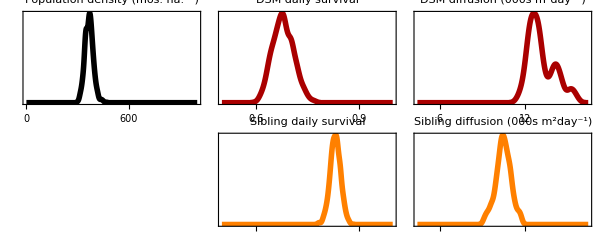

```mathematica
(*---------------------------Plot the Posterior distribution-----------------------------*)
(*---------------------------------------------------------------------------------------*)
(*------------Take samples 2000-10000, and thin by 10------------------*)
zz=2000;;10000;;10;
(*----------------------------------------------------------------------*)
(*---------------------Plot style options-------------------------------*)
th=0.01;
cols={{{Black,Dashing[0.05],Thickness[th]},{Black,Dashing[{0.1,0.05,0.02,0.05}],Thickness[th]},{Black,Thickness[th]}},{{Darker[Red],Dashing[0.05],Thickness[th]},{Darker[Red],Dashing[{0.1,0.05,0.02,0.05}],Thickness[th]},{Darker[Red],Thickness[th]}},{{Orange,Dashing[0.05],Thickness[th]},{Orange,Dashing[{0.1,0.05,0.02,0.05}],Thickness[th]},{Orange,Thickness[th]}},{{Darker[Red],Dashing[0.05],Thickness[th]},{Darker[Red],Dashing[{0.1,0.05,0.02,0.05}],Thickness[th]},{Darker[Red],Thickness[th]}},{{Orange,Dashing[0.05],Thickness[th]},{Orange,Dashing[{0.1,0.05,0.02,0.05}],Thickness[th]},{Orange,Thickness[th]}}};
ranges={{0,1000},{0.5,1},{0.5,1},{Log[5000],Log[20000]},{Log[5000],Log[20000]}};

tk={{{None,None},{Table[{i,i},{i,0,1000,200}],None}},{{None,None},{Automatic,None}},{{None,None},{Automatic,None}},
{{None,None},{Table[{Log[1000i],i},{i,{6,8,10,12,15,20}}],None}},{{None,None},{Table[{Log[1000i],i},{i,{6,8,10,12,15,20}}],None}}};
labs={"Population density (mos. ha.^-1)","DSM daily survival","Sibling daily survival","DSM diffusion (000s m^2day^-1)","Sibling diffusion (000s m^2day^-1)"};
(*----------------------------------------------------------------------*)
his=Table[SmoothHistogram[Map[If[ii<4,If[ii==1,10000#,#],Log[#]]&,resSW["ParameterRun"][[zz,ii]]],Automatic,"PDF",PlotRange->{ranges[[ii]],All},PlotStyle->cols[[ii,3]],PlotLabel->labs[[ii]],Frame->{True,True,False,False},FrameTicks->tk[[ii]]],{jj,2},{ii,5}];
figSW=GraphicsGrid[{his[[2,{1,2,4}]],{Null,his[[2,3]],his[[2,5]]}},ImageSize->600,Spacings->{-2,Automatic}]
```